# Defect Modular Bootstrap

## When the modular matrix has degeneracies modular bootstrap can only do so much to predict the the topological lines of the theory. Here we use a version of Breadth First Search to resolve the ambiguities.

## Modular Bootstrap

We will do this example on the folded Tricritical Ising CFT, but the parameters will be documented so that one can change them.

### Defining Folded Tricritical Ising Modular Data

```mathematica
(* Autosave because I've been burnt before *)
SetOptions[$FrontEnd,AutoSaveFrequency->1];
Get[FileNameJoin[{NotebookDirectory[],"math4ti2.m"}]];

(* A Timing Function *)
SetAttributes[Time,HoldFirst]
Time[x_]:=With[{res=AbsoluteTiming[x]},Echo[res[[1]],"Time: "];res[[2]]];

(* Define Tricritical Ising Parameters *)
FoldedMinimalModularData[p_:5,pp_:4]:= Module[
{cv,hv,sv,tv,H,i,ho,t,sMaker,s,nH,HIndex,svMat,tv2,twist},
cv=1-6(p-pp)^2/(p pp);(*//Echo[#,"c = "]&;*)
hv[r_,s_]:=hv[r,s]=((p r - pp s)^2-(p - pp)^2)/(4 p pp);
sv[a_,b_]:=sv[a,b]=2 (2/(p pp))^(1/2)(-1)^(1 + a[[2]]b[[1]]+a[[1]] b[[2]])Sin[π p/pp a[[1]] b[[1]]]Sin[π pp/p a[[2]] b[[2]]] ;
tv[a_,e_:1]:=tv[a,e]=ⅇ^(2 π ⅈ e(hv[a[[1]],a[[2]]]-cv/24));
H=Join[Flatten[Table[{r, s}, {r, 1, Floor[(pp-1)/2]}, {s, 1, p-1}], 1], If[EvenQ[pp], Table[{pp/2, s}, {s, 1, Floor[(p-1)/2]}], {}]];

(* Labels of folded Minimal Model primaries under the fixed point chiral algebra *)
i=({H[[Floor[#/2]]],H[[Floor[#/2]]],(-1)^#}& /@Range[2,2Length[H]+1])~Join~({#[[1]],#[[2]],0}&/@Subsets[H,{2}])~Join~({H[[Floor[#/2]]],H[[Floor[#/2]]],(-1)^# 2}& /@Range[2,2Length[H]+1]);

(* Their Conformal Weights *)
ho[a_]:=ho[a]=(hv@@(a[[1]])+hv@@(a[[2]])+a[[3]](a[[3]]-1)/2 + {{1,1},{1,1},-1}-a)(1-Abs[a[[3]]]-2)+((hv@@a[[1]])/2 +cv/24 3/2-(a[[3]]-2)/8 + {{1,1},{1,1},-2}-a)Abs[a[[3]]]-2//Simplify;

(* Modular T-Matrix *)
t=DiagonalMatrix[Exp[2π ⅈ(ho[#]-2 cv/24)]&/@i] // FullSimplify;

(*── Precomputed sv/tv tables for H×H ──────────────────────────────*)
nH=Length[H];
HIndex=AssociationThread[H->Range[nH]];
svMat=Table[sv[H[[a]],H[[b]]],{a,nH},{b,nH}];
tv2=Table[tv[H[[a]]]^2,{a,nH}];
twist[a1_,b1_]:=twist[a1,b1]=svMat[[HIndex[a1]]].(tv2*svMat[[All,HIndex[b1]]]);

(* This is the ugliest way I can write down the s-matrix of this thing *)
sMaker[a_,b_]:=sMaker[a,b]=Module[
{a1=a[[1]],a2=a[[2]],a3=a[[3]],b1=b[[1]],b2=b[[2]],b3=b[[3]]},
Which[a3==0&&b3==0,sv[a1,b1] sv[a2,b2]+sv[a1,b2] sv[a2,b1],
a3==0&&Abs[b3]==1,sv[a1,b1] sv[a2,b1],
Abs[a3]==1&&b3==0,sv[a1,b1] sv[a1,b2],
Abs[a3]==1&&Abs[b3]==1,1/2 sv[a1,b1]^2,
Abs[a3]==1&&Abs[b3]==2,1/2 a3 sv[a1,b1],
Abs[a3]==2&&Abs[b3]==1,1/2 b3 sv[a1,b1],
Abs[a3]==2&&Abs[b3]==2,1/8 a3 b3 twist[a1,b1] Exp[π ⅈ (hv@@a1+hv@@b1-cv/12)],
True,0]
];

s=Simplify[Array[sMaker[i[[#1]],i[[#2]]]&,{Length[i],Length[i]}],ComplexityFunction->LeafCount];
{s,t,i}
];
{s,t,i}=(Clear[s,t,i];FoldedMinimalModularData[5,4])//Time;

(* Modular Mass Matrix *)
z=Outer[(KroneckerDelta[#1,#2] + KroneckerDelta[#1[[1]],#2[[1]]]KroneckerDelta[#1[[2]],#2[[2]]]KroneckerDelta[#1[[3]],-#2[[3]]])(1-KroneckerDelta[Abs[#1[[3]]],2])(1-KroneckerDelta[Abs[#2[[3]]],2])&,i,i,1];
MatrixPlot[z,PlotLabel->"Modular Mass Matrix z"]
```

math4ti2: Mathematica interface to 4ti2 (http://www.4ti2.de/)
Copyright (C) 2017, Ralf Hemmecke <ralf@hemmecke.org>
Copyright (C) 2017, Silviu Radu <sradu@risc.jku.at>

Time:   0.969404

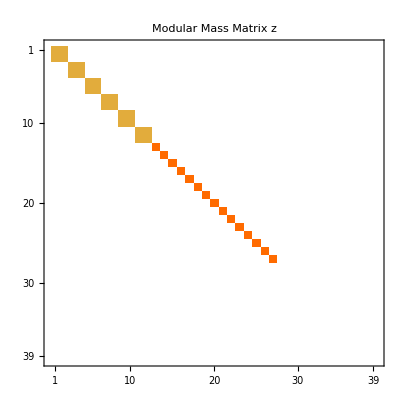

### Obtaining Modular Bootstrap Equations

```mathematica
SolveModularBootstrap[z_,s_]:=Module[
{X,x,nz, st=ConjugateTranspose[s],m,coeff,A, eqn,multipliers,basis},
Needs["math4ti2`"];

(* Get Nonzero positions on the Mass Matrix and replace them with variables *)
nz=Position[z, _?(# !=0 &)];
X=Array[x,Length[nz]];
m=st. ReplacePart[z,Thread[nz->X]] . s//Flatten;

(* Extract the coefficients for each variable in the S transformed Mass Matrix *)
coeff= CoefficientArrays[m,X][[2]]//Normal//N//Chop;

(* Pick the maximum number of independent equations and invert them *)
A=Chop@Inverse@N@coeff[[Flatten[FirstPosition[#,1]&/@DeleteCases[Chop@RowReduce@N@Transpose@coeff,{0..}]]]];

(* Plug them back in to the S-Transformed Modular Matrix to obtain constraints *)
m=Chop[N[coeff.A]].X;
(*A=RootApproximant[A];*)
eqn=DeleteDuplicates@Rationalize@Chop@Expand[#>=0&/@m];

(* Rescale any variables that need it so that the system has integer coefficients *)
multipliers=Min@Cases[eqn,(a_.*#)>=0:>a]^-1&/@X;
eqn=(#[[0]][Subtract@@#//ExpandAll,0])&/@(eqn/. Thread[X->multipliers*X]);

(* Use Z-Solve to find a basis of simple objects *)
basis =math4ti2`zsolve[eqn][[2]];

(A. (multipliers*#)&/@basis )/. a_?NumericQ/;!IntegerQ[a]:>ToRadicals@RootApproximant[a]
];
families=Sort[SolveModularBootstrap[z,s],#1[[1]] <= #2[[1]]&];//Time
families//Transpose//MatrixForm
noninvertibleFamilies=Select[families,#[[1]]!=1&];
```

Time:   2.31648

(1 | 1 | 1 | 1 | 1 | √2 | √2 | √2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 2 | √(3+√5) | √(3+√5) | √(3+√5) | √(3+√5) | √(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | √(7+3 √5) | √(7+3 √5) | √(2 (5+√5)) | √(2 (5+√5)) | √(2 (5+√5)) | √(2 (5+√5)) | 3+√5 | 2 √(5+√5) | 2 √(5+√5) | 2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(2 (5+2 √5)) | 2 √(2 (5+2 √5))
1 | 1 | 1 | -1 | -1 | √2 | √2 | -√2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 1/2 (-1-√5) | 2 | √(3+√5) | √(3+√5) | √(3+√5) | √(3+√5) | -√(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | √(7+3 √5) | √(7+3 √5) | -√(2 (5+√5)) | -√(2 (5+√5)) | √(2 (5+√5)) | √(2 (5+√5)) | 3+√5 | -2 √(5+√5) | 2 √(5+√5) | -2 √(5+2 √5) | -2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(5+2 √5) | -2 √(2 (5+2 √5)) | 2 √(2 (5+2 √5))
1 | 1 | 1 | -1 | -1 | √2 | √2 | -√2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 1/2 (-1-√5) | 2 | √(3+√5) | √(3+√5) | √(3+√5) | √(3+√5) | -√(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | √(7+3 √5) | √(7+3 √5) | √(2 (5+√5)) | √(2 (5+√5)) | -√(2 (5+√5)) | -√(2 (5+√5)) | 3+√5 | 2 √(5+√5) | -2 √(5+√5) | 2 √(5+2 √5) | 2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(5+2 √5) | 2 √(2 (5+2 √5)) | -2 √(2 (5+2 √5))
1 | 1 | 1 | 1 | 1 | √2 | √2 | √2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 2 | √(3+√5) | √(3+√5) | √(3+√5) | √(3+√5) | √(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | √(7+3 √5) | √(7+3 √5) | -√(2 (5+√5)) | -√(2 (5+√5)) | -√(2 (5+√5)) | -√(2 (5+√5)) | 3+√5 | -2 √(5+√5) | -2 √(5+√5) | -2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(2 (5+2 √5)) | -2 √(2 (5+2 √5))
1 | 1 | 1 | 1 | 1 | -√2 | -√2 | -√2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 2 | √(3-√5) | √(3-√5) | √(3-√5) | √(3-√5) | √(3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | -√(7-3 √5) | -√(7-3 √5) | √(2 (5-√5)) | √(2 (5-√5)) | √(2 (5-√5)) | √(2 (5-√5)) | 3-√5 | -2 √(5-√5) | -2 √(5-√5) | -2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(5-2 √5) | 2 √(2 (5-2 √5)) | 2 √(2 (5-2 √5))
1 | 1 | 1 | -1 | -1 | -√2 | -√2 | √2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 1/2 (-1+√5) | 2 | √(3-√5) | √(3-√5) | √(3-√5) | √(3-√5) | -√(3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | -√(7-3 √5) | -√(7-3 √5) | -√(2 (5-√5)) | -√(2 (5-√5)) | √(2 (5-√5)) | √(2 (5-√5)) | 3-√5 | 2 √(5-√5) | -2 √(5-√5) | 2 √(5-2 √5) | 2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(2 (5-2 √5)) | 2 √(2 (5-2 √5))
1 | 1 | 1 | -1 | -1 | -√2 | -√2 | √2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 1/2 (-1+√5) | 2 | √(3-√5) | √(3-√5) | √(3-√5) | √(3-√5) | -√(3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | -√(7-3 √5) | -√(7-3 √5) | √(2 (5-√5)) | √(2 (5-√5)) | -√(2 (5-√5)) | -√(2 (5-√5)) | 3-√5 | -2 √(5-√5) | 2 √(5-√5) | -2 √(5-2 √5) | -2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(2 (5-2 √5)) | -2 √(2 (5-2 √5))
1 | 1 | 1 | 1 | 1 | -√2 | -√2 | -√2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 2 | √(3-√5) | √(3-√5) | √(3-√5) | √(3-√5) | √(3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | -√(7-3 √5) | -√(7-3 √5) | -√(2 (5-√5)) | -√(2 (5-√5)) | -√(2 (5-√5)) | -√(2 (5-√5)) | 3-√5 | 2 √(5-√5) | 2 √(5-√5) | 2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(5-2 √5) | -2 √(2 (5-2 √5)) | -2 √(2 (5-2 √5))
1 | 1 | 1 | 1 | 1 | √2 | √2 | √2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 2 | -√(3-√5) | -√(3-√5) | -√(3-√5) | -√(3-√5) | -√(3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | √(7-3 √5) | √(7-3 √5) | √(2 (5-√5)) | √(2 (5-√5)) | √(2 (5-√5)) | √(2 (5-√5)) | 3-√5 | 2 √(5-√5) | 2 √(5-√5) | -2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(2 (5-2 √5)) | -2 √(2 (5-2 √5))
1 | 1 | 1 | -1 | -1 | √2 | √2 | -√2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 1/2 (-1+√5) | 2 | -√(3-√5) | -√(3-√5) | -√(3-√5) | -√(3-√5) | √(3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | √(7-3 √5) | √(7-3 √5) | -√(2 (5-√5)) | -√(2 (5-√5)) | √(2 (5-√5)) | √(2 (5-√5)) | 3-√5 | -2 √(5-√5) | 2 √(5-√5) | 2 √(5-2 √5) | 2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(5-2 √5) | 2 √(2 (5-2 √5)) | -2 √(2 (5-2 √5))
1 | 1 | 1 | -1 | -1 | √2 | √2 | -√2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 1/2 (-1+√5) | 2 | -√(3-√5) | -√(3-√5) | -√(3-√5) | -√(3-√5) | √(3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | √(7-3 √5) | √(7-3 √5) | √(2 (5-√5)) | √(2 (5-√5)) | -√(2 (5-√5)) | -√(2 (5-√5)) | 3-√5 | 2 √(5-√5) | -2 √(5-√5) | -2 √(5-2 √5) | -2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(5-2 √5) | -2 √(2 (5-2 √5)) | 2 √(2 (5-2 √5))
1 | 1 | 1 | 1 | 1 | √2 | √2 | √2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 2 | -√(3-√5) | -√(3-√5) | -√(3-√5) | -√(3-√5) | -√(3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | √(7-3 √5) | √(7-3 √5) | -√(2 (5-√5)) | -√(2 (5-√5)) | -√(2 (5-√5)) | -√(2 (5-√5)) | 3-√5 | -2 √(5-√5) | -2 √(5-√5) | 2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(2 (5-2 √5)) | 2 √(2 (5-2 √5))
1 | 1 | 1 | 1 | 1 | -√2 | -√2 | -√2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 2 | -√(3+√5) | -√(3+√5) | -√(3+√5) | -√(3+√5) | -√(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | -√(7+3 √5) | -√(7+3 √5) | √(2 (5+√5)) | √(2 (5+√5)) | √(2 (5+√5)) | √(2 (5+√5)) | 3+√5 | -2 √(5+√5) | -2 √(5+√5) | 2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(5+2 √5) | -2 √(2 (5+2 √5)) | -2 √(2 (5+2 √5))
1 | 1 | 1 | -1 | -1 | -√2 | -√2 | √2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 1/2 (-1-√5) | 2 | -√(3+√5) | -√(3+√5) | -√(3+√5) | -√(3+√5) | √(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | -√(7+3 √5) | -√(7+3 √5) | -√(2 (5+√5)) | -√(2 (5+√5)) | √(2 (5+√5)) | √(2 (5+√5)) | 3+√5 | 2 √(5+√5) | -2 √(5+√5) | -2 √(5+2 √5) | -2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(2 (5+2 √5)) | -2 √(2 (5+2 √5))
1 | 1 | 1 | -1 | -1 | -√2 | -√2 | √2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 1/2 (-1-√5) | 2 | -√(3+√5) | -√(3+√5) | -√(3+√5) | -√(3+√5) | √(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | -√(7+3 √5) | -√(7+3 √5) | √(2 (5+√5)) | √(2 (5+√5)) | -√(2 (5+√5)) | -√(2 (5+√5)) | 3+√5 | -2 √(5+√5) | 2 √(5+√5) | 2 √(5+2 √5) | 2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(2 (5+2 √5)) | 2 √(2 (5+2 √5))
1 | 1 | 1 | 1 | 1 | -√2 | -√2 | -√2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 2 | -√(3+√5) | -√(3+√5) | -√(3+√5) | -√(3+√5) | -√(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | -√(7+3 √5) | -√(7+3 √5) | -√(2 (5+√5)) | -√(2 (5+√5)) | -√(2 (5+√5)) | -√(2 (5+√5)) | 3+√5 | 2 √(5+√5) | 2 √(5+√5) | -2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(5+2 √5) | 2 √(2 (5+2 √5)) | 2 √(2 (5+2 √5))
1 | 1 | -1 | 1 | -1 | 0 | 0 | 0 | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 1/2 (-1-√5) | 1/2 (1+√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (-3-√5) | 0 | 0 | 0 | √(5+√5) | -√(5+√5) | √(5+√5) | -√(5+√5) | 0 | 0 | 0 | -√(2 (5+2 √5)) | √(2 (5+2 √5)) | √(2 (5+2 √5)) | -√(2 (5+2 √5)) | 0 | 0
1 | 1 | -1 | -1 | 1 | 0 | 0 | 0 | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (-3-√5) | 0 | 0 | 0 | -√(5+√5) | √(5+√5) | √(5+√5) | -√(5+√5) | 0 | 0 | 0 | √(2 (5+2 √5)) | -√(2 (5+2 √5)) | √(2 (5+2 √5)) | -√(2 (5+2 √5)) | 0 | 0
1 | 1 | -1 | -1 | 1 | 0 | 0 | 0 | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (-3-√5) | 0 | 0 | 0 | √(5+√5) | -√(5+√5) | -√(5+√5) | √(5+√5) | 0 | 0 | 0 | -√(2 (5+2 √5)) | √(2 (5+2 √5)) | -√(2 (5+2 √5)) | √(2 (5+2 √5)) | 0 | 0
1 | 1 | -1 | 1 | -1 | 0 | 0 | 0 | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 1/2 (-1-√5) | 1/2 (1+√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (-3-√5) | 0 | 0 | 0 | -√(5+√5) | √(5+√5) | -√(5+√5) | √(5+√5) | 0 | 0 | 0 | √(2 (5+2 √5)) | -√(2 (5+2 √5)) | -√(2 (5+2 √5)) | √(2 (5+2 √5)) | 0 | 0
1 | 1 | -1 | 1 | -1 | 0 | 0 | 0 | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 1/2 (-1+√5) | 1/2 (1-√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (-3+√5) | 0 | 0 | 0 | √(5-√5) | -√(5-√5) | √(5-√5) | -√(5-√5) | 0 | 0 | 0 | √(2 (5-2 √5)) | -√(2 (5-2 √5)) | -√(2 (5-2 √5)) | √(2 (5-2 √5)) | 0 | 0
1 | 1 | -1 | -1 | 1 | 0 | 0 | 0 | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (-3+√5) | 0 | 0 | 0 | -√(5-√5) | √(5-√5) | √(5-√5) | -√(5-√5) | 0 | 0 | 0 | -√(2 (5-2 √5)) | √(2 (5-2 √5)) | -√(2 (5-2 √5)) | √(2 (5-2 √5)) | 0 | 0
1 | 1 | -1 | -1 | 1 | 0 | 0 | 0 | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (-3+√5) | 0 | 0 | 0 | √(5-√5) | -√(5-√5) | -√(5-√5) | √(5-√5) | 0 | 0 | 0 | √(2 (5-2 √5)) | -√(2 (5-2 √5)) | √(2 (5-2 √5)) | -√(2 (5-2 √5)) | 0 | 0
1 | 1 | -1 | 1 | -1 | 0 | 0 | 0 | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 1/2 (-1+√5) | 1/2 (1-√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (-3+√5) | 0 | 0 | 0 | -√(5-√5) | √(5-√5) | -√(5-√5) | √(5-√5) | 0 | 0 | 0 | -√(2 (5-2 √5)) | √(2 (5-2 √5)) | √(2 (5-2 √5)) | -√(2 (5-2 √5)) | 0 | 0
2 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | -4 | √10 | -√10 | -√10 | √10 | 0 | -2 | -2 | -2 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 2 | 2 | 0 | 0 | 2 √2 | 2 √2 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 4 | √2 | √2 | √2 | √2 | 0 | -2 | -2 | -2 | 2 | -2 √2 | -2 √2 | 0 | 0 | 0 | 0 | -4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 1+√5 | 1+√5 | 1+√5 | 1+√5 | 0 | 0 | -4 | 0 | 0 | 0 | 0 | 0 | 3+√5 | 3+√5 | 3+√5 | -2-2 √5 | 0 | 0 | 0 | 0 | 0 | 0 | -6-2 √5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | -2 | 0 | 0 | 0 | √2 | -√2 | 0 | 0 | 1+√5 | -1-√5 | 0 | 0 | 0 | 0 | √(3+√5) | -√(3+√5) | √(3+√5) | -√(3+√5) | 0 | -3-√5 | 3+√5 | 0 | 0 | -√(7+3 √5) | √(7+3 √5) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | -2 | 0 | 0 | 0 | √2 | -√2 | 0 | √5 | 1 | -1 | -√5 | 0 | 0 | 0 | √(3+√5) | √(3-√5) | -√(3-√5) | -√(3+√5) | 0 | 2 | -2 | 0 | 0 | √2 | -√2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 1-√5 | 1-√5 | 1-√5 | 1-√5 | 0 | 0 | -4 | 0 | 0 | 0 | 0 | 0 | 3-√5 | 3-√5 | 3-√5 | -2+2 √5 | 0 | 0 | 0 | 0 | 0 | 0 | -6+2 √5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 2 | 2 | 0 | 0 | -2 √2 | -2 √2 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 4 | -√2 | -√2 | -√2 | -√2 | 0 | -2 | -2 | -2 | 2 | 2 √2 | 2 √2 | 0 | 0 | 0 | 0 | -4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | -2 | 0 | 0 | 0 | -√2 | √2 | 0 | -√5 | 1 | -1 | √5 | 0 | 0 | 0 | √(3-√5) | √(3+√5) | -√(3+√5) | -√(3-√5) | 0 | 2 | -2 | 0 | 0 | -√2 | √2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | -2 | 0 | 0 | 0 | -√2 | √2 | 0 | 0 | 1-√5 | -1+√5 | 0 | 0 | 0 | 0 | √(3-√5) | -√(3-√5) | √(3-√5) | -√(3-√5) | 0 | -3+√5 | 3-√5 | 0 | 0 | √(7-3 √5) | -√(7-3 √5) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | -4 | -√10 | √10 | √10 | -√10 | 0 | -2 | -2 | -2 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | -2 | 0 | 0 | 0 | √2 | -√2 | 0 | -√5 | 1 | -1 | √5 | 0 | 0 | 0 | -√(3-√5) | -√(3+√5) | √(3+√5) | √(3-√5) | 0 | 2 | -2 | 0 | 0 | √2 | -√2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | -2 | 0 | 0 | 0 | √2 | -√2 | 0 | 0 | 1-√5 | -1+√5 | 0 | 0 | 0 | 0 | -√(3-√5) | √(3-√5) | -√(3-√5) | √(3-√5) | 0 | -3+√5 | 3-√5 | 0 | 0 | -√(7-3 √5) | √(7-3 √5) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | -2 | 0 | 0 | 0 | -√2 | √2 | 0 | 0 | 1+√5 | -1-√5 | 0 | 0 | 0 | 0 | -√(3+√5) | √(3+√5) | -√(3+√5) | √(3+√5) | 0 | -3-√5 | 3+√5 | 0 | 0 | √(7+3 √5) | -√(7+3 √5) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | -2 | 0 | 0 | 0 | -√2 | √2 | 0 | √5 | 1 | -1 | -√5 | 0 | 0 | 0 | -√(3+√5) | -√(3-√5) | √(3-√5) | √(3+√5) | 0 | 2 | -2 | 0 | 0 | -√2 | √2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 2 | -2 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | -2 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

## Resolving Ambiguities

As we can see from the answers above for part of the primaries the action of the defects is ambiguous and we really only know the trace. Yet we have a lot of data, perhaps enough to fully constrain the action on the primaries (up to a basis choice). To do this we will use fusion rules. These are highly constrained also simply by looking at the action in the nondegenerate primaries. Then we will search fusion rules for consistencies using a version of BFS.

### Defect Manipulations

Since we don’t need a really big matrix to store the action of the defects, we will instead opt to store them using a list of 1x1 and 2x2 matrices depending on which are ambiguous or not. So we can define an associative operation for the tensor product!!

```mathematica
(* Define a Defect Fusion Product Operation *)
SetAttributes[CircleTimes,{Flat,OneIdentity}]
a_ ⊗ b_:=MapThread[Which[MatrixQ[#1]&&MatrixQ[#2],#1.#2,True,#1*#2]&,{a,b}];
CircleTimes[a_,b_,rest__]:=CircleTimes[CircleTimes[a,b],rest]

(* A couple of helper functions that can be applied to Lines *)
tr[x_]:=Which[MatrixQ[x],Tr[x],True,x];
inv[x_]:=Which[MatrixQ[x],Inverse[x],True,1/x];
dual[x_]:=Which[MatrixQ[x],ConjugateTranspose[x],True,Conjugate[x]];
SuperDagger[x_]:=dual/@x;
ShowLine[L_]:=MatrixForm[MatrixForm/@L];

(* This mask tells us if the current primary is degenerate *)
degMask=Thread[families[[1]]!=1];
degPos=Flatten@Position[degMask,True];
nondegPos=Flatten@Position[Not/@degMask,True];
deg[x_]:=degMask[[x]];
degNum=Total@Boole@degMask;
primNum=Total@Boole@degMask;
famNum=Length@families;
familiesNondeg=families[[All,nondegPos]];degeneracy[i_Integer]:=families[[1,i]];
```

### Invertible Lines

```mathematica
GetInvertibleLines[]:=Module[
{i={{1,0},{0,1}},
a={{1,0},{0,-1}},
b={{0,1},{1,0}},
c={{ⅈ,0},{0,-ⅈ}},
(*c={{0,1},{-1,0}},*)
L1,Lσ,Lχ},
L1={1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,i,i,i,i,i,i,i,i,i,i,i,i,i,i,i};
Lσ={1,-1,-1,1,1,-1,-1,1,1,-1,-1,1,1,-1,-1,1,1,-1,-1,1,1,-1,-1,1,a,a,a,b,b,a,a,b,b,a,b,b,b,b,a};
Lχ={1,-1,-1,1,1,-1,-1,1,1,-1,-1,1,1,-1,-1,1,-1,1,1,-1,-1,1,1,-1,a,a,a,c,c,a,a,c,c,a,c,c,c,c,-a};
{L1,Lχ⊗Lχ,Lχ⊗Lσ,Lσ⊗Lχ,Lσ,Lσ⊗Lχ⊗Lχ,Lχ,Lχ⊗Lχ⊗Lχ}
];

(* Extract the invertible Lines *)
Li=GetInvertibleLines[];
L=GetInvertibleLines[];
solvedFamilies=<|
1->{Li[[1]]},
2->{Li[[2]]},
3->Li[[3;;4]],
4->Li[[5;;6]],
5->Li[[7;;8]]
|>;
SolvedQ[x_Integer,solvedFamilies_:solvedFamilies]:=KeyExistsQ[solvedFamilies,x];

(* Takes a list of lines and appends them to the solved families *)
UpdateSolvedLines[lines_]:=
(line|->Module[
{traces=tr/@line,fam},
If[!MemberQ[L,line],
AppendTo[L,line];
fam=First@FirstPosition[N[families],N[traces],Missing,1];
solvedFamilies[fam]=Append[Lookup[solvedFamilies,fam,{}],line];
]
])/@lines;

(* Functions to create a defect with free variables and given traces, as well to extract the variables *)
l[var_Symbol]:=Array[Module[{n=degeneracy[#]},Which[n==1,var[#],True,Table[var[#,n*(i-1) + j],{i,n},{j,n}]]]&,famNum];
(*l[var_Symbol]:=Array[Module[{n=degeneracy[#]},Which[n==1,var[#,1]+ⅈ var[#,2],True,Table[var[#,2n*(i-1) + 2j -1] + ⅈ var[#,2n*(i-1) + 2j],{i,n},{j,n}]]]&,famNum];*)
l[traces_List,var_]:=MapThread[Which[!MatrixQ[#2],#1,True,Module[{n=Length[#2],mat=#2},mat[[n,n]]=#1-Tr[mat[[;;n-1,;;n-1]]];mat ]]&,{traces,l[var]},1];
```

### Gauge Fixing

```mathematica
(* Obtain a general Gauge Transformation that preserves the solved Lines *)
GetGeneralGaugeTransform[L_,var_:P]:=Module[{Lp,LpInvertibleQ,Lpp},
(* Build a General Gauge Transformation *)
Lp=l[var](*Array[Which[!deg[#],1,deg[#],{{var[#,1] ,var[#,2] },{var[#,3],var[#,4]}}]&,famNum]*);
Lp=(Lp //.{ToRules[Reduce[And@@Thread[Flatten[(Lp⊗# -#⊗Lp)&/@L]==0],Backsubstitution->True]]});
Lpp=Variables[Lp];

(* Checks if Lp is invertible for a given numerical set of P variables *)
Module[{
vars=Table[Unique["p"],Length@Lpp],
invertibleLp=And@@((Simplify@Not@Reduce[Or@@(Which[MatrixQ[#],Det[#]==0,True,#==0]&/@#)])&/@Lp)
},
invertibleLp=invertibleLp/.Thread[Lpp->vars];
LpInvertibleQ:=Function@@{vars,Simplify[Evaluate[invertibleLp]]}
];
{Lp,Lpp,LpInvertibleQ}
];
{Lp,Lpp,LpInvertibleQ}=GetGeneralGaugeTransform[L,P];
```

```mathematica
(* These are Queries for if a line is related by conjugation of invertible defects, or by a change of Gauge, or both *)
Clear[conjugateOrbit,invertibleOrbit,gaugeNullSpace,fusionOrbit,bilinearFusionOrbit];
conjugateOrbit[x_,Li_:Li]:=conjugateOrbit[x,Li]=DeleteDuplicates[Simplify[#⊗x⊗(inv/@#)]&/@Li];
fusionOrbit[x_,L_:L]:=fusionOrbit[x,L]=DeleteDuplicates[Simplify[#⊗x&/@L]];
bilinearFusionOrbit[x_,L_:L]:=bilinearFusionOrbit[x,L]=DeleteDuplicates[Simplify[Flatten[Outer[#1⊗x⊗#2&,L,L,1,1],1]]];
invertibleOrbit[x_,Li_:Li]:=invertibleOrbit[x,Li]=Module[
{trace=Chop@N[tr/@x]},
Select[bilinearFusionOrbit[x,Li],trace == Chop@N[tr/@#]&]
];

(* Calculates the nullspace of the Jacobian of Lp x - x Lp, and if it is empty then there is no gauge transformation *)
gaugeNullSpace[x_,y_,Lp_:Lp,Lpp_:Lpp]:=gaugeNullSpace[x,y,Lp,Lpp]=(NullSpace@Outer[D,Flatten[ExpandAll[#⊗x-y⊗#]],Lpp])&/@Lp;
GaugeQ[x_,y_,Lp_:Lp,Lpp_:Lpp,LpInvertibleQ_:LpInvertibleQ]:=Module[
{ns,dummies},
ns=gaugeNullSpace[x,y,Lp,Lpp];
Or@@(Which[
#==={},False,
Length@# ===Length@Lpp,True,
True,
dummies=Array[x,Length@#];
Assuming[Thread[Variables[{x,y,dummies}]!=0],Simplify[LpInvertibleQ@@(dummies.#)]]
]&/@ns)];

(* Solves system quietly ignoring the cases when parameters are undetermined *)
QuietSolve[eqn_,vars_]:=Quiet[Solve[eqn,vars],{Solve::svars,Solve::fulldim,Solve::ratnz}];

(* Cleans up some variables *)
CanonicalizeVars[list_]:=Array[i|->Module[{vars},
vars=Variables[list[[i]]];
list[[i]]/.MapIndexed[#->#[[0]][i,#2[[1]]]&,vars]],
Length@list];

(* Given a defect with free variables, it outputs a list of the variables that are pure gauge *)
GaugeParams[x_]:=Module[
{vars=Variables[x]},
Pick[vars,Simplify[GaugeQ[x,x/. #->z]&/@vars,Assumptions->Flatten[{Thread[vars!=0],z!=0}]]]
];
AllGaugeQ[x_]:=Flatten[First/@BooleanVariables[FunctionDomain[Flatten[x],Variables[x]]]]===Flatten[GaugeParams[x]];

(* Given a Matrix for a gauge transformation this calculates traceless Lie Algebra generators *)
LieGenerators[x_]:=Which[MatrixQ[x],Module[
{II=IdentityMatrix[Length[x]],vars=Variables[x]},
DeleteCases[#-Tr[#]/2 II&/@(D[x,#]&/@vars),0*II]
],True,{}];

(* Takes a defect x and a parameterized Gauge Transformation Lp and returns the relations needed to put x in a fixed gauge *)
(*GaugeFixingRelations[x_,Lp_:Lp[[1]]]:=Simplify@And@@MapThread[{A,P}|->Module[
{generators=LieGenerators[P]},
Which[generators==={},True,
True,Reduce[Thread[Tr[ConjugateTranspose[#].A]&/@generators==0]]
]
],{x,Lp}];*)

GaugeFixingRelations[x_,Lp_:Lp[[1]]]:=Simplify@And@@MapThread[{A,P}|->Module[
{generators=LieGenerators[P]},
Which[!MatrixQ[A],True,
generators==={},True,
DiagonalMatrixQ[P]&&SameQ@@Diagonal[P],True,
MatrixQ[P]&&DiagonalMatrixQ[P],Reduce[And@@Flatten[Table[If[i!=j,A[[i,j]]==A[[j,i]],Nothing],{i,Length[A]},{j,Length[A]}]]],
True,Reduce[Thread[(Tr[ConjugateTranspose[#].A]&/@generators)==0]]]],{x,Lp}];

(* Spits out a Defect after we have gaugefixed a bunch of parameters *)
GaugeFix[x_,Lp_:Lp[[1]]]:=(x/.Solve[GaugeFixingRelations[x,Lp]])[[1]];
lGaugeFixed[var_Symbol,Lp_List:Lp]:=GaugeFix[l[var],Lp[[1]]];
lGaugeFixed[traces_List,var_Symbol,Lp_List:Lp]:=GaugeFix[l[traces,var],Lp[[1]]];
```

### Orbit Fixing

```mathematica
(* Given a function f and a group G, checks if f(G A G) == f(A) *)
CheckInvariant[f_,A_,G_]:=AllTrue[Tuples[{G,G}],Expand[f[A]-f[#[[1]].A.#[[2]]]]===0&];
CheckInvariantFast[m_,orbitSubstitutions_]:=AllTrue[orbitSubstitutions,Expand[m-(m/.#)]===0&];

(* Obtain symbolic expresssions for a generating set of invariants under the orbit of some lines *)
(* Optimization: Have Z-Solve solve the bigger matrix instead *)
Needs["math4ti2`"];
ClearAll[OrbitInvariantsSingle];
OrbitInvariantsSingle[A_,G_,upToOrder_]:=OrbitInvariantsSingle[A,G,upToOrder]=Module[
{vars =Variables[A],monomials,flatA=Flatten[A],orbitSubstitutions,invariantMonomials,exponents,basis},
(* Calculate a lot of monomials in the variables of A, and find which ones are invariant under the group action *)
monomials=DeleteCases[MonomialList[(1+Total[vars])^upToOrder],1];

orbitSubstitutions=Thread[flatA->Flatten[#]]&/@((#[[1]].A.#[[2]]) &/@ Tuples[{G,G}]);
invariantMonomials=Sort[Select[monomials,CheckInvariantFast[#,orbitSubstitutions]&]];

(* Solve for the minimum algebraically independent polynomials by finding a Hilbert basis on the exponents *)
exponents=Exponent[#, vars]&/@invariantMonomials;
basis=math4ti2`hilbert[exponents][[1]];

(* Convert Back to symbols *)
Echo[Times @@@(vars^#&/@basis),G]
];
OrbitInvariants[x_,defects_,upToOrder_Integer:4]:=OrbitInvariants[x,defects,upToOrder]=MapThread[{A,G}|->Which[MatrixQ[A],OrbitInvariantsSingle[A,G,upToOrder],True,{}]
,{x,Transpose[defects]}];

(* Somtimes invariants can be related to each other, this calculates their relations *)
ClearAll[Syzygies];
Syzygies[invariants_]:=Syzygies[invariants]=Module[
{varsGauge=Variables[invariants],vars=Table[Unique["a"],Length@invariants]},
#==0&/@GroebnerBasis[MapThread[Equal,{invariants,vars}],vars,varsGauge]
];

(* Calculate the invariants for the invertible lines up to Gauge Transformation *)
ll=lGaugeFixed[x];
llflat=Flatten[ll];
invertibleInvariants=OrbitInvariants[ll,Li];
InvertibleInvariants=Function[x,invertibleInvariants/.Thread[llflat->Flatten[x]]];
invertibleSyzygies=Syzygies/@invertibleInvariants;

(* Check if two lines are in the same orbit *)
Clear[InvertibleOrbitQ];
InvertibleOrbitQ[x_,y_]:=InvertibleOrbitQ[x,y]=AllTrue[Flatten@Expand[InvertibleInvariants[x]-InvertibleInvariants[y]],#===0&];

(* *)

(* A solve function that uses orbit fixing to speed things up *)
QuietSolveOrbitFixed[eqns_,orbitInvariants_,vars_]:=Module[
{orbitVars=Array[a,Length@orbitInvariants],orbitEqns,orbitSols,syzygies =Syzygies[orbitInvariants]},

(* Solve the equation in invariant space *)
orbitEqns=GroebnerBasis[
Join[
(List@@eqns)/. Equal[a_,b_]:>a-b,
MapThread[#1-#2&,{orbitInvariants,orbitVars}]
],
orbitVars,
vars,
MonomialOrder->EliminationOrder];

orbitSols= QuietSolve[#==0&/@orbitEqns,orbitVars];

First@QuietSolve[Join[
MapThread[Equal,{orbitVars,orbitInvariants}]/.#,
#==0&/@syzygies
],vars]&/@orbitSols
];


(* A solve function that uses orbit fixing to speed things up *)
QuietSolveOrbitFixed[eqns_,orbitInvariants_,vars_]:=Module[
{reVars=Array[a,Length@vars],imVars=Array[b,Length@vars],compVars,expandRules,orbitVars,invariants,equations,orbitEqns,orbitSols,syzygies},
compVars=Join[reVars,imVars];
expandRules=Thread[vars->reVars+ⅈ imVars];
(*invariants=DeleteCases[Assuming[Thread[compVars∈Reals],Simplify[Join[Re[#],Im[#]]&[ComplexExpand[orbitInvariants/.expandRules]]]],0];*)
invariants=DeleteCases[Assuming[Thread[compVars∈Reals],ComplexExpand[orbitInvariants/.expandRules]],0];
orbitVars=Array[p,Length@invariants];
syzygies =Syzygies[invariants];
equations=DeleteCases[Assuming[Thread[compVars∈Reals],ComplexExpand[Flatten[(List@@@eqns)/. Equal[a_,b_]:>a-b]/.expandRules]],0];

(* Solve the equation in invariant space *)
orbitEqns=GroebnerBasis[
Join[
equations,
MapThread[#1-#2&,{invariants,orbitVars}]
],
orbitVars,
compVars,
MonomialOrder->EliminationOrder];
(*Echo[Thread[orbitVars->invariants],syzygies];
Echo[equations];
Echo[orbitEqns];*)
orbitSols= QuietSolve[#==0&/@orbitEqns,orbitVars];
(First@QuietSolve[Join[
MapThread[Equal,{orbitVars,invariants}]/.#,
#==0&/@syzygies
],compVars]&/@orbitSols)
];
```

{{{1,0},{0,1}},{{1,0},{0,1}},{{1,0},{0,1}},{{1,0},{0,1}},{{1,0},{0,-1}},{{1,0},{0,-1}},{{1,0},{0,-1}},{{1,0},{0,-1}}}  {x[25,1],x[25,2]^2,x[25,4]^2}

{{{1,0},{0,1}},{{1,0},{0,1}},{{1,0},{0,1}},{{1,0},{0,1}},{{1,0},{0,-1}},{{1,0},{0,-1}},{{1,0},{0,-1}},{{1,0},{0,-1}}}  {x[26,1],x[26,2]^2,x[26,4]^2}

{{{1,0},{0,1}},{{1,0},{0,1}},{{1,0},{0,1}},{{1,0},{0,1}},{{1,0},{0,-1}},{{1,0},{0,-1}},{{1,0},{0,-1}},{{1,0},{0,-1}}}  {x[27,1],x[27,2]^2,x[27,4]^2}

{{{1,0},{0,1}},{{-1,0},{0,-1}},{{0,ⅈ},{-ⅈ,0}},{{0,-ⅈ},{ⅈ,0}},{{0,1},{1,0}},{{0,-1},{-1,0}},{{ⅈ,0},{0,-ⅈ}},{{-ⅈ,0},{0,ⅈ}}}  {x[28,1] x[28,2] x[28,3] x[28,4]}

{{{1,0},{0,1}},{{-1,0},{0,-1}},{{0,ⅈ},{-ⅈ,0}},{{0,-ⅈ},{ⅈ,0}},{{0,1},{1,0}},{{0,-1},{-1,0}},{{ⅈ,0},{0,-ⅈ}},{{-ⅈ,0},{0,ⅈ}}}  {x[29,1] x[29,2] x[29,3] x[29,4]}

{{{1,0},{0,1}},{{1,0},{0,1}},{{1,0},{0,1}},{{1,0},{0,1}},{{1,0},{0,-1}},{{1,0},{0,-1}},{{1,0},{0,-1}},{{1,0},{0,-1}}}  {x[30,1],x[30,2]^2,x[30,4]^2}

{{{1,0},{0,1}},{{1,0},{0,1}},{{1,0},{0,1}},{{1,0},{0,1}},{{1,0},{0,-1}},{{1,0},{0,-1}},{{1,0},{0,-1}},{{1,0},{0,-1}}}  {x[31,1],x[31,2]^2,x[31,4]^2}

{{{1,0},{0,1}},{{-1,0},{0,-1}},{{0,ⅈ},{-ⅈ,0}},{{0,-ⅈ},{ⅈ,0}},{{0,1},{1,0}},{{0,-1},{-1,0}},{{ⅈ,0},{0,-ⅈ}},{{-ⅈ,0},{0,ⅈ}}}  {x[32,1] x[32,2] x[32,3] x[32,4]}

{{{1,0},{0,1}},{{-1,0},{0,-1}},{{0,ⅈ},{-ⅈ,0}},{{0,-ⅈ},{ⅈ,0}},{{0,1},{1,0}},{{0,-1},{-1,0}},{{ⅈ,0},{0,-ⅈ}},{{-ⅈ,0},{0,ⅈ}}}  {x[33,1] x[33,2] x[33,3] x[33,4]}

{{{1,0},{0,1}},{{1,0},{0,1}},{{1,0},{0,1}},{{1,0},{0,1}},{{1,0},{0,-1}},{{1,0},{0,-1}},{{1,0},{0,-1}},{{1,0},{0,-1}}}  {x[34,1],x[34,2]^2,x[34,4]^2}

{{{1,0},{0,1}},{{-1,0},{0,-1}},{{0,ⅈ},{-ⅈ,0}},{{0,-ⅈ},{ⅈ,0}},{{0,1},{1,0}},{{0,-1},{-1,0}},{{ⅈ,0},{0,-ⅈ}},{{-ⅈ,0},{0,ⅈ}}}  {x[35,1] x[35,2] x[35,3] x[35,4]}

{{{1,0},{0,1}},{{-1,0},{0,-1}},{{0,ⅈ},{-ⅈ,0}},{{0,-ⅈ},{ⅈ,0}},{{0,1},{1,0}},{{0,-1},{-1,0}},{{ⅈ,0},{0,-ⅈ}},{{-ⅈ,0},{0,ⅈ}}}  {x[36,1] x[36,2] x[36,3] x[36,4]}

{{{1,0},{0,1}},{{-1,0},{0,-1}},{{0,ⅈ},{-ⅈ,0}},{{0,-ⅈ},{ⅈ,0}},{{0,1},{1,0}},{{0,-1},{-1,0}},{{ⅈ,0},{0,-ⅈ}},{{-ⅈ,0},{0,ⅈ}}}  {x[37,1] x[37,2] x[37,3] x[37,4]}

{{{1,0},{0,1}},{{-1,0},{0,-1}},{{0,ⅈ},{-ⅈ,0}},{{0,-ⅈ},{ⅈ,0}},{{0,1},{1,0}},{{0,-1},{-1,0}},{{ⅈ,0},{0,-ⅈ}},{{-ⅈ,0},{0,ⅈ}}}  {x[38,1] x[38,2] x[38,3] x[38,4]}

{{{1,0},{0,1}},{{1,0},{0,1}},{{-1,0},{0,-1}},{{-1,0},{0,-1}},{{1,0},{0,-1}},{{1,0},{0,-1}},{{-1,0},{0,1}},{{-1,0},{0,1}}}  {x[39,1]^2,x[39,2]^2,x[39,4]^2}

```mathematica
vars={x[1,1],x[1,2],x[1,3],x[1,4],x[1,5],x[1,6],x[1,7]};
eqns={Conjugate[x[1,1]] x[1,1]==2&&Conjugate[x[1,2]]+x[1,2]==0&&Conjugate[x[1,2]] x[1,2]==0&&Conjugate[x[1,3]] x[1,3]==2&&Conjugate[x[1,4]] x[1,4]==2&&Conjugate[x[1,5]]+x[1,5]==0&&Conjugate[x[1,5]] x[1,5]==0&&Conjugate[x[1,6]] x[1,6]==2&&Conjugate[x[1,7]] x[1,7]==0};
invs={x[1,1]^2,x[1,2]^2,x[1,3]^2,x[1,4]^2,x[1,5]^2,x[1,6]^2,x[1,7]^2};
out=List@@QuietSolveOrbitFixed[eqns,invs,vars]//Time
```

Time:   0.106305

{{b[1]→ⅈ a[1]-√(-p[1]),b[2]→ⅈ a[2],b[3]→ⅈ a[3]-√(-p[3]),b[4]→ⅈ a[4]-√(-p[4]),b[5]→ⅈ a[5],b[6]→ⅈ a[6]-√(-p[6]),b[7]→ⅈ a[7]-√(-p[7])}}

```mathematica
res1//.out
```

{res1}

### Search Fusion Rules

Since we can obtain some partial information for the fusion rules among defects belonging to each family we can extract and list them in the following

```mathematica
(* Takes a matrix M and a vector v and finds all possible nonnegative integer combinations of rows of M that sum to v *)
FindIntegerCombinations[M_,v_]:=Module[
{n=Length[M],m=Length[v],MT=Transpose[N[M]],ubounds, enumerate,results={}},

(* Use linear programming to estimate the maximum number a row can be added in a solution for v *)
ubounds=Table[Module[{sol},
sol=Quiet[LinearProgramming[-UnitVector[n,i],MT,Transpose[{N[v],ConstantArray[0,m]}],ConstantArray[0,n]]];
If[VectorQ[sol],Max[0,sol[[i]]//Chop//RootApproximant],sol]]
,{i,n}];

(* Explore the rest recursively until you hit zero *)
enumerate[rem_,idx_,current_]:=Which[idx>n,If[Chop[N[rem]]==ConstantArray[0,m],AppendTo[results,current]],True,Do[enumerate[rem-k*M[[idx]],idx+1,Append[current,k]],{k,0,ubounds[[idx]]}]];
enumerate[v,1,{}];
results
];
Clear[FindIntegerCombinationsCached];
FindIntegerCombinationsCached[M_,v_]:=FindIntegerCombinationsCached[M,v]=FindIntegerCombinations[M,v];
```

## Solving with Existing Lines

As we keep going through families with higher and higher quantum dimension we can use existing lines to constrain new ones. This is a variation of constrain with invertible lines, but this time it uses the full might of the already solved families. We will do an extra optimization. Since once a family is solved we know all the lines there and not just the traces,  this places a much stricter constraint on what the results of fusions can be other than their traces.

```mathematica
(* Find possible integer combinations for a defect with unknown variables *)
PossibleSimpleDecompositions[trace_]:=Module[
{vars=Variables[trace],indices},
Which[
Length[vars]==0,
FindIntegerCombinationsCached[families,trace],
True,
indices=Flatten@Position[trace, _?(FreeQ[#,Alternatives@@vars]&),{1},Heads->False];
FindIntegerCombinationsCached[families[[All,indices]],trace[[indices]]]
]
];

(* Uses trace equations and known lines to produce candidates for the unknown parameters *)
ReduceDecompositions[defect_,trace_,decompositions_]:=Or@@(decomp|->Module[
{sparseDecomp=SparseArray[decomp],indices},
indices=sparseDecomp["NonzeroPositions"][[All,1]];
Which[
(* If the fusion is in one family and it has been solved equate them cell by cell *)
And[Length[indices]==1,SolvedQ[indices[[1]]]],
BooleanConvert[Or@@(And@@DeleteCases[Expand[MapThread[Equal,{Flatten[defect],Flatten[#]}]],True]&/@solvedFamilies[indices[[1]]]),"DNF"],
(* Otherwise equate their traces *)
True,
BooleanConvert[And@@DeleteCases[Expand[MapThread[Equal,{Flatten[trace],decomp.families},1]],True],"DNF"]
]])/@decompositions;


ConstraintsFromKnown[defect_,L_:L]:=Module[
{vars=Variables[defect],products,traces,decompositions,result},

(* Calculate the possible fusion channels with the known defects *)
products=fusionOrbit[defect,L];
traces=tr/@#&/@products;
decompositions=PossibleSimpleDecompositions/@traces;

(* Obtain a system of equations and reduce it *)
decompositions=And@@DeleteDuplicates[MapThread[ReduceDecompositions,{products, traces, decompositions}]]
(*DeleteDuplicates[DeleteDuplicates/@Simplify/@(List@@#&/@List@@decompositions)]*)
]
```

```mathematica
eqToPoly[Equal[a_,b_]]:=a-b

parseSystem[expr_]:=Module[
{topArgs,flatGens,orBlocks},
(*Unwrap top-level And (or treat single expr as a 1-element list)*)
topArgs=If[Head[expr]===And,List@@expr,{expr}];

(*Flat generators:top-level equalities only*)
flatGens=eqToPoly/@Cases[topArgs,_Equal];
(*OR blocks:each Or becomes a list of per-branch generator lists*)
orBlocks=Map[Function[orExpr,
Map[Function[branch,
Switch[Head[branch],
And,eqToPoly/@Cases[List@@branch,_Equal],
Equal,{eqToPoly[branch]},
True,{},
_,{}
]
],List@@orExpr]],
(*branches of this Or*)
Cases[topArgs,_Or]];
{flatGens,orBlocks}]
```

```mathematica
SetAttributes[x,NHoldAll];
fam=families[[20]];
def=l[fam,x];
(*ShowLine@def*)
res1=ConstraintsFromKnown[def,L]//Time;
polynomialBasis=res1//parseSystem//Time;
OrbitInvariants[def,Li]//Flatten//Time
```

Time:   0.042926

Time:   0.001029

{{{1,0},{0,1}},{{1,0},{0,1}},{{1,0},{0,1}},{{1,0},{0,1}},{{1,0},{0,-1}},{{1,0},{0,-1}},{{1,0},{0,-1}},{{1,0},{0,-1}}}  {x[25,1],x[25,2]^2,x[25,3]^2}

{{{1,0},{0,1}},{{1,0},{0,1}},{{1,0},{0,1}},{{1,0},{0,1}},{{1,0},{0,-1}},{{1,0},{0,-1}},{{1,0},{0,-1}},{{1,0},{0,-1}}}  {x[26,1],x[26,2]^2,x[26,3]^2}

{{{1,0},{0,1}},{{1,0},{0,1}},{{1,0},{0,1}},{{1,0},{0,1}},{{1,0},{0,-1}},{{1,0},{0,-1}},{{1,0},{0,-1}},{{1,0},{0,-1}}}  {x[27,1],x[27,2]^2,x[27,3]^2}

{{{1,0},{0,1}},{{-1,0},{0,-1}},{{0,ⅈ},{-ⅈ,0}},{{0,-ⅈ},{ⅈ,0}},{{0,1},{1,0}},{{0,-1},{-1,0}},{{ⅈ,0},{0,-ⅈ}},{{-ⅈ,0},{0,ⅈ}}}  {}

{{{1,0},{0,1}},{{-1,0},{0,-1}},{{0,ⅈ},{-ⅈ,0}},{{0,-ⅈ},{ⅈ,0}},{{0,1},{1,0}},{{0,-1},{-1,0}},{{ⅈ,0},{0,-ⅈ}},{{-ⅈ,0},{0,ⅈ}}}  {}

{{{1,0},{0,1}},{{1,0},{0,1}},{{1,0},{0,1}},{{1,0},{0,1}},{{1,0},{0,-1}},{{1,0},{0,-1}},{{1,0},{0,-1}},{{1,0},{0,-1}}}  {x[30,1],x[30,2]^2,x[30,3]^2}

{{{1,0},{0,1}},{{1,0},{0,1}},{{1,0},{0,1}},{{1,0},{0,1}},{{1,0},{0,-1}},{{1,0},{0,-1}},{{1,0},{0,-1}},{{1,0},{0,-1}}}  {x[31,1],x[31,2]^2,x[31,3]^2}

{{{1,0},{0,1}},{{-1,0},{0,-1}},{{0,ⅈ},{-ⅈ,0}},{{0,-ⅈ},{ⅈ,0}},{{0,1},{1,0}},{{0,-1},{-1,0}},{{ⅈ,0},{0,-ⅈ}},{{-ⅈ,0},{0,ⅈ}}}  {}

{{{1,0},{0,1}},{{-1,0},{0,-1}},{{0,ⅈ},{-ⅈ,0}},{{0,-ⅈ},{ⅈ,0}},{{0,1},{1,0}},{{0,-1},{-1,0}},{{ⅈ,0},{0,-ⅈ}},{{-ⅈ,0},{0,ⅈ}}}  {}

{{{1,0},{0,1}},{{1,0},{0,1}},{{1,0},{0,1}},{{1,0},{0,1}},{{1,0},{0,-1}},{{1,0},{0,-1}},{{1,0},{0,-1}},{{1,0},{0,-1}}}  {x[34,1],x[34,2]^2,x[34,3]^2}

{{{1,0},{0,1}},{{-1,0},{0,-1}},{{0,ⅈ},{-ⅈ,0}},{{0,-ⅈ},{ⅈ,0}},{{0,1},{1,0}},{{0,-1},{-1,0}},{{ⅈ,0},{0,-ⅈ}},{{-ⅈ,0},{0,ⅈ}}}  {}

{{{1,0},{0,1}},{{-1,0},{0,-1}},{{0,ⅈ},{-ⅈ,0}},{{0,-ⅈ},{ⅈ,0}},{{0,1},{1,0}},{{0,-1},{-1,0}},{{ⅈ,0},{0,-ⅈ}},{{-ⅈ,0},{0,ⅈ}}}  {}

{{{1,0},{0,1}},{{-1,0},{0,-1}},{{0,ⅈ},{-ⅈ,0}},{{0,-ⅈ},{ⅈ,0}},{{0,1},{1,0}},{{0,-1},{-1,0}},{{ⅈ,0},{0,-ⅈ}},{{-ⅈ,0},{0,ⅈ}}}  {}

«1 more identical outputs»

{{{1,0},{0,1}},{{1,0},{0,1}},{{-1,0},{0,-1}},{{-1,0},{0,-1}},{{1,0},{0,-1}},{{1,0},{0,-1}},{{-1,0},{0,1}},{{-1,0},{0,1}}}  {x[39,1]^2,x[39,2]^2,x[39,3]^2}

Time:   0.554621

{x[25,1],x[25,2]^2,x[25,3]^2,x[26,1],x[26,2]^2,x[26,3]^2,x[27,1],x[27,2]^2,x[27,3]^2,x[30,1],x[30,2]^2,x[30,3]^2,x[31,1],x[31,2]^2,x[31,3]^2,x[34,1],x[34,2]^2,x[34,3]^2,x[39,1]^2,x[39,2]^2,x[39,3]^2}

```mathematica
Variables[def]
```

{x[25,1],x[25,2],x[25,3],x[26,1],x[26,2],x[26,3],x[27,1],x[27,2],x[27,3],x[28,1],x[28,2],x[28,3],x[29,1],x[29,2],x[29,3],x[30,1],x[30,2],x[30,3],x[31,1],x[31,2],x[31,3],x[32,1],x[32,2],x[32,3],x[33,1],x[33,2],x[33,3],x[34,1],x[34,2],x[34,3],x[35,1],x[35,2],x[35,3],x[36,1],x[36,2],x[36,3],x[37,1],x[37,2],x[37,3],x[38,1],x[38,2],x[38,3],x[39,1],x[39,2],x[39,3]}

```mathematica
def
```

{√(3+√5),-√(3+√5),-√(3+√5),√(3+√5),√(3-√5),-√(3-√5),-√(3-√5),√(3-√5),-√(3-√5),√(3-√5),√(3-√5),-√(3-√5),-√(3+√5),√(3+√5),√(3+√5),-√(3+√5),0,0,0,0,0,0,0,0,{{x[25,1],x[25,2]},{x[25,3],-x[25,1]}},{{x[26,1],x[26,2]},{x[26,3],-x[26,1]}},{{x[27,1],x[27,2]},{x[27,3],-x[27,1]}},{{x[28,1],x[28,2]},{x[28,3],-x[28,1]}},{{x[29,1],x[29,2]},{x[29,3],-x[29,1]}},{{x[30,1],x[30,2]},{x[30,3],-x[30,1]}},{{x[31,1],x[31,2]},{x[31,3],-x[31,1]}},{{x[32,1],x[32,2]},{x[32,3],-x[32,1]}},{{x[33,1],x[33,2]},{x[33,3],-x[33,1]}},{{x[34,1],x[34,2]},{x[34,3],-x[34,1]}},{{x[35,1],x[35,2]},{x[35,3],-x[35,1]}},{{x[36,1],x[36,2]},{x[36,3],-x[36,1]}},{{x[37,1],x[37,2]},{x[37,3],-x[37,1]}},{{x[38,1],x[38,2]},{x[38,3],-x[38,1]}},{{x[39,1],x[39,2]},{x[39,3],-x[39,1]}}}

# OLD

```mathematica
ConstrainWithKnown[defect_,L_:L]:=Module[
{vars=Variables[defect],products,traces,decompositions,result},

(* Calculate the possible fusion channels with the known defects *)
products=fusionOrbit[defect,L];
traces=tr/@#&/@products;
decompositions=PossibleSimpleDecompositions/@traces;

(* Obtain a system of equations and reduce it *)
decompositions=Simplify@Reduce/@MapThread[ReduceDecompositions,{products, traces, decompositions}];
(*result=(defect//.#)&/@(QuietSolve[decompositions,vars]);*)
result=DeleteDuplicates[defect//.{Simplify@Reduce/@N[decompositions] //DeleteDuplicates//Reduce//ToRules}];

(* Convert numerical constants back to algebraic form, preserving variables *)
(*result=result/. a_?NumericQ/;!IntegerQ[a]:>RootApproximant[a,4];*)
result=result/. a_?NumericQ/;!IntegerQ[a]:>ToRadicals@RootApproximant[a];
CanonicalizeVars@DeleteDuplicates[result,InvertibleOrbitQ]
];
```

## Constraining with Dual Fusion

Each defect must fuse with its dual such that it produces the identity. In a unitary representation the dual is given by the conjugate transpose, and therefore we can impose this as a consistency condition as well.

```mathematica
(* Constrain using fusion with their dual *)
ConstrainWithDualFusion[defects_,Li_:Li]:=Module[
{vars=Variables[defects],products,traces,decompositions,orbitInvariants,result},

(* Calculate Fusion among members of family *)
products=Simplify[Flatten[{((#⊗ SuperDagger[#]-Li[[1]])),((SuperDagger[#]⊗ #-Li[[1]]))}&/@defects,1]];
(*Echo[ShowLine/@products];*)
traces=tr/@#&/@products;
(*Echo[ShowLine/@traces];*)

(* Constrain their possible fusion pathways and turn them into equations using their traces *)
decompositions=PossibleSimpleDecompositions/@traces;
(*Echo[decompositions];*)
decompositions=Simplify[MapThread[ReduceDecompositions,{products, traces, decompositions}]]//DeleteDuplicates;
Echo[decompositions];
orbitInvariants=OrbitInvariants[#,Li]&/@defects//Flatten;
Echo[orbitInvariants,"Invariants: "];
result=DeleteDuplicates[Flatten[(defects//.#)&/@(QuietSolveOrbitFixed[And@@decompositions,orbitInvariants,vars]),1]];

(* Convert numerical constants back to algebraic form, preserving variables *)
(*result=result/. a_?NumericQ/;!IntegerQ[a]:>RootApproximant[a,4];*)
CanonicalizeVars@DeleteDuplicates[Simplify@result,InvertibleOrbitQ]
];
```

## Constraining with Self Fusion

The last condition we will impose is the fusion of the defects among themselves. In particular, if we have a collection of defects, their products should all have fusion decompositions in our fusion ring. This will help us pinpoint the remaining gauge degrees of freedom.

```mathematica
(* Constrain using fusion among thesemeves *)
ConstrainWithSelfFusion[defects_]:=Module[
{vars=Variables[defects],products,traces,decompositions,result},

(* Calculate Fusion among members of family *)
products=DeleteDuplicates[Flatten[Outer[#1⊗#2&,defects,defects,1,1],1]];
traces=tr/@#&/@products;

(* Constrain their possible fusion pathways and turn them into equations using their traces *)
decompositions=PossibleSimpleDecompositions/@traces;
decompositions=MapThread[ReduceDecompositions,{products, traces, decompositions}];
result=Flatten[(defects//.#)&/@(QuietSolve[N[decompositions],vars]),1];

(* Convert numerical constants back to algebraic form, preserving variables *)
result=result/. a_?NumericQ/;!IntegerQ[a]:>RootApproximant[a,4];
CanonicalizeVars@DeleteDuplicates[Simplify@result,InvertibleOrbitQ]
];
```

```mathematica
SetAttributes[x,NHoldAll];
fam=families[[6]];
def=lGaugeFixed[fam,x,Lp];
(*ShowLine@def*)
res1=ConstrainWithKnown[def,L]//Simplify//Time;
ShowLine/@res1
res=ConstrainWithDualFusion[res1]//Time;
Echo[Variables[res],"Remaining Variables: "];
ShowLine/@res
```

Time:   0.143396

{(√2
√2
√2
√2
-√2
-√2
-√2
-√2
√2
√2
√2
√2
-√2
-√2
-√2
-√2
0
0
0
0
0
0
0
0
(0 | x[1,1]
x[1,1] | 0)
(√2 | x[1,2]
x[1,2] | √2)
(0 | x[1,3]
x[1,3] | 0)
(1/(√2) | -ⅈ/(√2)
ⅈ/(√2) | 1/(√2))
(1/(√2) | -ⅈ/(√2)
ⅈ/(√2) | 1/(√2))
(0 | x[1,4]
x[1,4] | 0)
(-√2 | x[1,5]
x[1,5] | -√2)
(-1/(√2) | ⅈ/(√2)
-ⅈ/(√2) | -1/(√2))
(-1/(√2) | ⅈ/(√2)
-ⅈ/(√2) | -1/(√2))
(0 | x[1,6]
x[1,6] | 0)
(1/(√2) | -ⅈ/(√2)
ⅈ/(√2) | 1/(√2))
(1/(√2) | -ⅈ/(√2)
ⅈ/(√2) | 1/(√2))
(-1/(√2) | ⅈ/(√2)
-ⅈ/(√2) | -1/(√2))
(-1/(√2) | ⅈ/(√2)
-ⅈ/(√2) | -1/(√2))
(0 | x[1,7]
x[1,7] | 0))}

{Conjugate[x[1,1]] x[1,1]==2&&Conjugate[x[1,2]]+x[1,2]==0&&Conjugate[x[1,2]] x[1,2]==0&&Conjugate[x[1,3]] x[1,3]==2&&Conjugate[x[1,4]] x[1,4]==2&&Conjugate[x[1,5]]+x[1,5]==0&&Conjugate[x[1,5]] x[1,5]==0&&Conjugate[x[1,6]] x[1,6]==2&&Conjugate[x[1,7]] x[1,7]==0}

Invariants:   {x[1,1]^2,x[1,2]^2,x[1,3]^2,x[1,4]^2,x[1,5]^2,x[1,6]^2,x[1,7]^2}

Join::heads: Heads And and List at positions 1 and 2 are expected to be the same.

Solve::nsmet: This system cannot be solved with the methods available to Solve. Try Reduce or FindInstance instead.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Join::heads: Heads ReplaceAll and List at positions 1 and 2 are expected to be the same.

Solve::naqs: … is not a quantified system of equations and inequalities.

ReplaceAll::reps: {p[1],p[2],p[3],p[4],p[5],p[6],p[7]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Join::heads: Heads ReplaceAll and List at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

Solve::naqs: Join[{p[1]==a[1]^2+2 ⅈ a[1] b[1]-b[«1»]^2,p[2]==a[2]^2+2 ⅈ a[2] b[2]-b[«1»]^2,p[3]==a[3]^2+2 ⅈ a[3] b[3]-b[«1»]^2,p[4]==a[4]^2+2 ⅈ a[4] b[4]-b[«1»]^2,p[5]==a[5]^2+2 ⅈ a[5] b[5]-b[«1»]^2,p[6]==a[6]^2+2 ⅈ a[6] b[6]-b[«1»]^2,p[7]==a[7]^2+2 ⅈ a[7] b[7]-b[«1»]^2}/.{p[1],p[2],p[3],p[4],p[5],p[6],p[7]},{}] is not a quantified system of equations and inequalities.

Solve::naqs: … is not a quantified system of equations and inequalities.

General::stop: Further output of Solve::naqs will be suppressed during this calculation.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceRepeated::reps: {Join[{p[1]==x[1,1]^2,p[2]==x[1,2]^2,p[3]==x[1,3]^2,p[4]==x[1,4]^2,p[5]==x[1,5]^2,p[6]==x[1,6]^2,p[7]==x[1,7]^2}/.{Join[False,{Plus[«2»],Plus[«2»],Plus[«2»],Plus[«2»],Plus[«2»],Plus[«2»],Plus[«2»]}]==0},{}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceRepeated::reps: {Join[{p[1]==x[1,1]^2,p[2]==x[1,2]^2,p[3]==x[1,3]^2,p[4]==x[1,4]^2,p[5]==x[1,5]^2,p[6]==x[1,6]^2,p[7]==x[1,7]^2}/.{p[1],p[2],p[3],p[4],p[5],p[6],p[7]},{}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceRepeated::reps: {1} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceRepeated::reps will be suppressed during this calculation.

Time:   0.46124

Remaining Variables:   {1//.1,2//.1}

ReplaceRepeated::reps: {1} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{1//.1,2//.1}